```mathematica
x=Import["./nuevosdatos.mat","Table"]//ToExpression;
```

```mathematica
x//Dimensions
```

{40,12}

```mathematica
x[[1]]
```

{4.70332,4.49553,-0.85748,3.35488,4.20395,6.90628,4.64826,4.61854,2.21415,2.55699,4.19903,5.83247}

```mathematica
Import["/home/david/libs/QuantumDavid.m"]
```

```mathematica
campo=linearmesh[0,Pi/2,40]
```

{0,π/78,π/39,π/26,(2 π)/39,(5 π)/78,π/13,(7 π)/78,(4 π)/39,(3 π)/26,(5 π)/39,(11 π)/78,(2 π)/13,π/6,(7 π)/39,(5 π)/26,(8 π)/39,(17 π)/78,(3 π)/13,(19 π)/78,(10 π)/39,(7 π)/26,(11 π)/39,(23 π)/78,(4 π)/13,(25 π)/78,π/3,(9 π)/26,(14 π)/39,(29 π)/78,(5 π)/13,(31 π)/78,(16 π)/39,(11 π)/26,(17 π)/39,(35 π)/78,(6 π)/13,(37 π)/78,(19 π)/39,π/2}

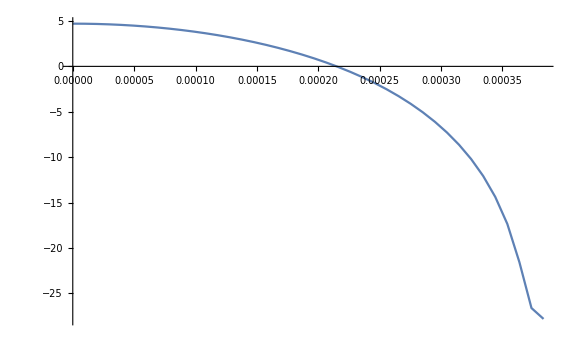
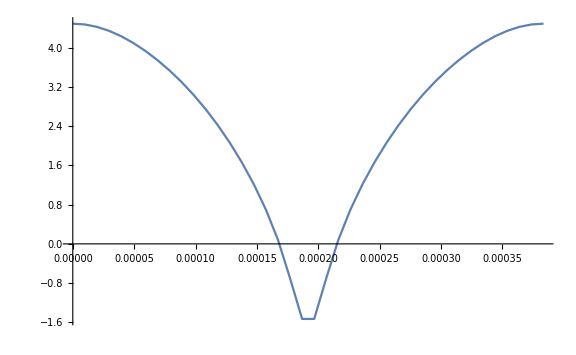
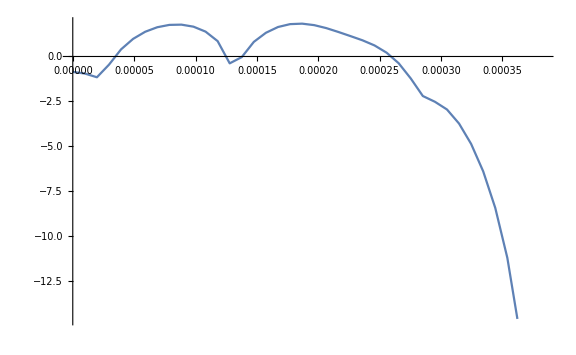
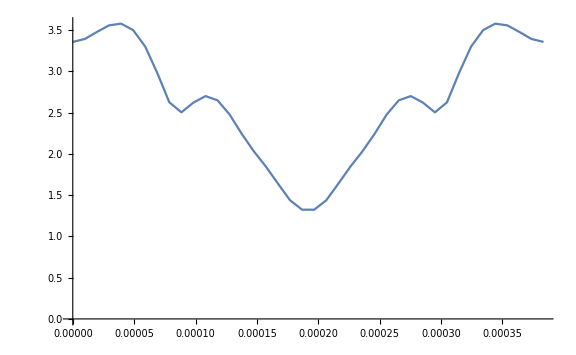
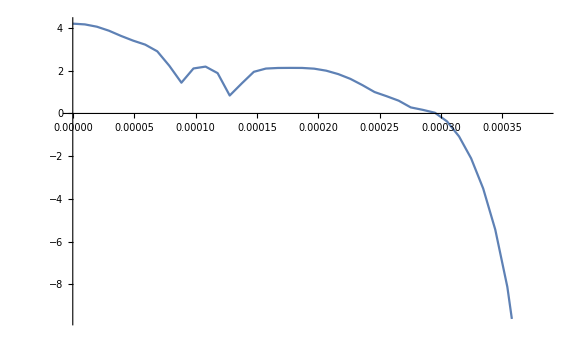
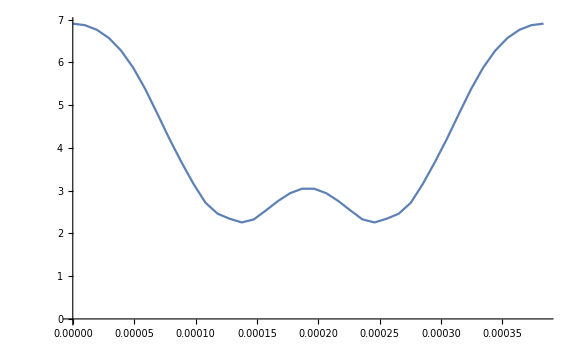
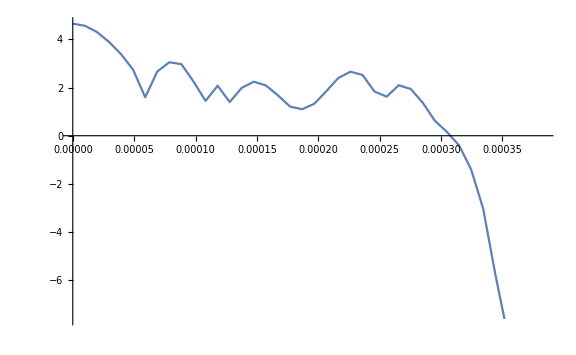
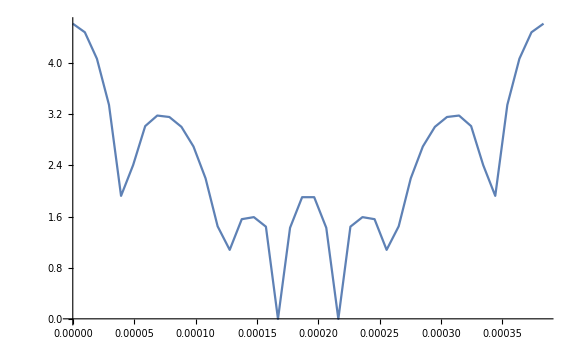

```mathematica
dan=Table[ListLinePlot[Table[{campo[[k]]/2^12,x[[k]][[i]]},{k,1,40}],ImageSize->Large],{i,1,12}]
```

```mathematica
?Show
```

RowBox[{"Show", "[", RowBox[{StyleBox["graphics", "TI"], ",", StyleBox["options", "TI"]}], "]"}] shows graphics with the specified options added. 
RowBox[{"Show", "[", RowBox[{SubscriptBox[StyleBox["g", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["g", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] shows several graphics combined.

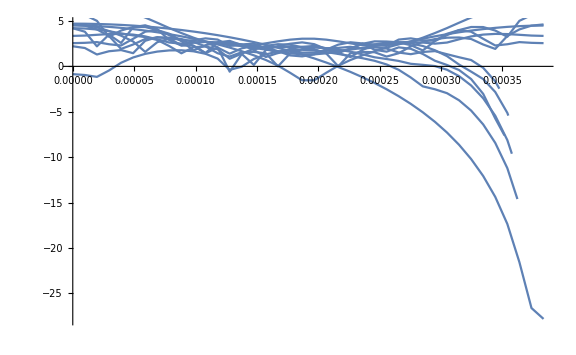

```mathematica
Show[dan]
```